```mathematica
SetDirectory[NotebookDirectory[]];
SingularPoints=Import["SingularPoints.csv","CSV"];
CentralFlow=Import["UC_Trajectories_Central.csv","CSV"];
IncFlow=Import["UC_Trajectories_Inc.csv","CSV"];
OuterFlow=Import["UC_Trajectories_Outer.csv","CSV"];
```

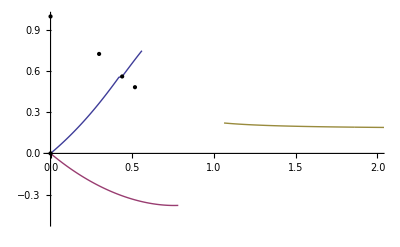

```mathematica
ListLinePlot[{IncFlow,OuterFlow,CentralFlow},PlotRange->{{0,2},{-0.5,1}},Epilog->Map[Point,SingularPoints]]
```

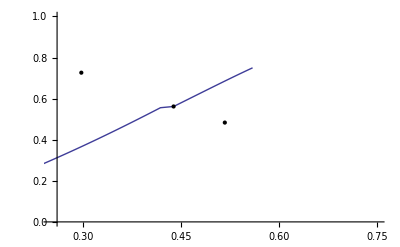

```mathematica
ListLinePlot[{IncFlow,OuterFlow,CentralFlow},PlotRange->{{0.25,0.75},{-0.,1}},Epilog->Map[Point,SingularPoints]]
```